```mathematica
Clear[ss2,ss,ssd]
ss[j_, x_,c_] := ss[j,x,c]=ss[j-1,x,c]+ j^(-1/2)Sin[c+x Log[j]]
ss[0,x_,c_]:=0
ssa[j_, x_,c_] := j^(-1/2)Sin[c+x Log[j]]
ss2[n_,j_,x_,c_] := ss2[n,j,x,c]=ss2[n,j-1,x,c]+ j^(-1/2)Sin[c+x Log[j/n]]
ss2[n_,0,x_,c_]:=0
ss3[j_, x_,c_] := ss3[j,x,c]=ss3[j-1,x,c]+ j^(-1/2)Sin[c x j]
ss3[0,x_,c_]:=0
```

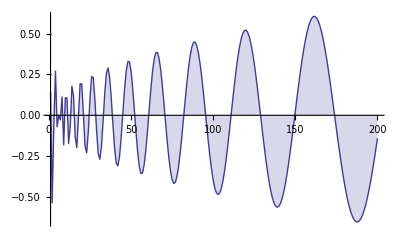

```mathematica
DiscretePlot[ ss[n,N@Im[ZetaZero[2]],3],{n,1,200}]
```

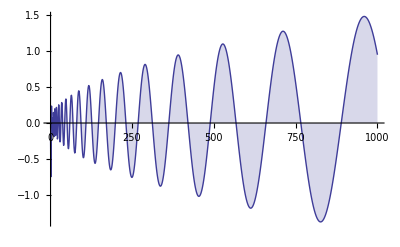

```mathematica
DiscretePlot[ ss2[1000,k,N@Im[ZetaZero[2]],4],{k,1,1000}]
```

```mathematica
Animate[DiscretePlot[Re[ ss[n,N@Im[ZetaZero[5]],x]],{n,1,200}],{x,0,6.28}]
```

```mathematica
Animate[DiscretePlot[ ss[n,N@Im[ZetaZero[300]],x],{n,1,1000}],{x,0,6.28}]
```

```mathematica
Animate[DiscretePlot[ ss2[10000,n,N@Im[ZetaZero[300]],x],{n,1,1000}],{x,0,6.28}]
```

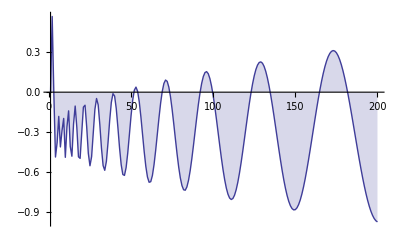

```mathematica
DiscretePlot[ ss[n,.3+N@Im[ZetaZero[2]],0],{n,1,200}]
```

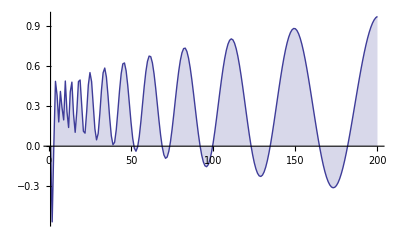

```mathematica
DiscretePlot[ ss[n,.3+N@Im[ZetaZero[2]],Pi],{n,1,200}]
```

```mathematica
Animate[DiscretePlot[ Re@ss[n,N@Im[ZetaZero[3800]],x],{n,1,1000},PlotRange->4],{x,0,6.28}]
```

```mathematica
N[ZetaZero[3800]]
```

0.5+4314.8 ⅈ

```mathematica
Animate[DiscretePlot[ Re@ssd[n,N@Im[ZetaZero[1]],x],{n,1,1000},PlotRange->4],{x,0,6.28}]
```

```mathematica
j^(-1/2)/.j->10
```

1/(√10)

```mathematica
E^(-1/2Log[j])/.j->10
```

1/(√10)

```mathematica
Expand[1/(2I)E^(-1/2Log[j])(E^(I(x Log[j]+c))-E^(-I(x Log[j]+c)))]
```

1/2 ⅈ ⅇ^(-ⅈ c) j^(-1/2-ⅈ x)-1/2 ⅈ ⅇ^(ⅈ c) j^(-1/2+ⅈ x)

```mathematica
-Sin[1.]
```

-0.841471

```mathematica
Sin[1. + Pi]
```

-0.841471

```mathematica
Animate[DiscretePlot[ Re@ss4[n,N@ZetaZero@1,x I],{n,1,400}],{x,0,6.28}]
```